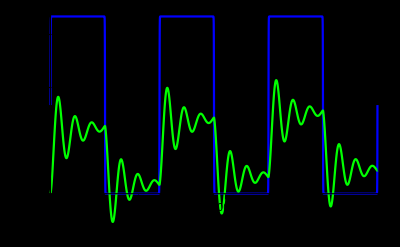

```mathematica
ClearAll["Global*`"];

(* počáteční data součástek *)
R1 = 3.3 * 10^3;
R2 = 47 * 10^3;
C1 = 39 * 10^-9;
C2 = 82 * 10^-9;
L = 22 * 10^-3;

amplituda = 5;
frekvence = 1 * 10^3;
uz[t_] := amplituda*(1+Tanh[100 Sin[2*Pi*frekvence*t]])/2;

rovnice = {
iR1[t] + iL[t] == iU[t] + iR2[t],
0 == iR1[t] + iL[t] + iC1[t],
iC1[t] + iR2[t] == iC2[t],

uz[t] == u1[t],
u2[t] - u1[t] == R1 * iR1[t],
u1[t] - u3[t] == R2 * iR2[t],
u2[t] - u1[t] == L * iL'[t],
iC1[t] == C1 * (u2'[t] - u3'[t]),
iC2[t] == C2 * u3'[t],

u2[0] == 0,
u3[0] == 0,
iL[0] == 0
};

tmax = 3* (1/frekvence); (* vykreslíme 3 periody *)

(* Nyní soustavu rovnic vyřešíme - následující řádky jsou Copy-Paste *)

nezname = Union[Cases[rovnice, _Symbol[t], {0, Infinity}]];
reseni = NDSolve[rovnice, nezname, {t, 0, tmax}, StartingStepSize-> 10^-9];

(* Vykreslení grafu - pozor na parametry *)
Plot[{uz[t] /. reseni[[1]], u3[t] /. reseni[[1]]}, {t, 0, tmax}, PlotStyle -> {Blue, Green}, PlotLegends -> "u3(t)", Background -> Black, PlotRange -> All]
```